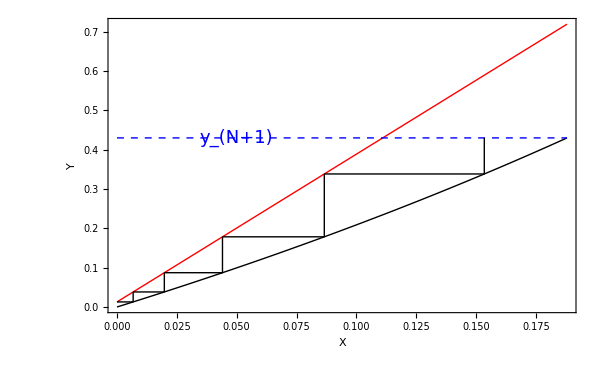
-Graphics- | in = 430. kmol/h
out = 489.515 kmol/h

```mathematica
Module[{x0,y1,yN1,yeq,xeq,LVmin,LV,V,L,yop,X,Y,n,xN,plot,eq},
x0=0;y1=0.0129;yN1=0.43;

yeq[x_]:=(1.9*x)/(1-0.9*x);

xeq=x/.Quiet@Solve[yeq[x]==yN1,x][[1]];
LVmin=(yN1-y1)/(xeq-x0);
LV=1.4*LVmin;

V=1000;L=LV*V;
(*yop[x_]:=LV*(x-x0)+y1;*)
yop[x_]:=3.757*x+y1;

X[0]=x0;Y[0]=y1;
Do[{X[i]=x/.Quiet@Solve[yeq[x]==Y[i-1],x][[1]],Y[i]=yop[X[i]]},{i,1,20}];
n=DeleteCases[If[yeq[X[#]]>yN1,0,#]&/@Range@20,0][[-1]];
xN=X[n];

plot=Plot[{yeq[x],yop[x]},{x,0,xeq},PlotStyle->{{Thick,Black},{Thick,Red}},PlotRangePadding->None,
Frame->True,FrameLabel->{Style["X",Italic],Style["Y",Italic]},LabelStyle->{17,Black},ImageSize->{600,400},
Epilog->{Thick,
{Blue,Dashed,Line[{{0,yN1},{xeq,yN1}}],Text[Style[Subscript[Style["y",Italic],Row@{Style["N",Italic],"+1"}],18,Background->White],{0.05,yN1}]},
Line[{{X[#-1],Y[#-1]},{X[#],Y[#-1]},{X[#],Y[#]}}]&/@Range[n-1],
Line[{{X[n-1],Y[n-1]},{X[n],Y[n-1]},{X[n],yN1}}]
}];

eq=Text@Style[Column[{
Row@{"in = ",x0*L+yN1*V," kmol/h"},
Row@{"out = ",xN*L+y1*V," kmol/h"}
},Alignment->"="],18];

Grid@{{plot,eq}}
]
```